### Soliton

```mathematica
t=0;
ClearAll[A]
ρ = 1060.;
E0 = 3.7 10^9;
nu = 0.34;
l = -18.9 10^9;
m = -13.3 10^9;
n = -10. 10^9;
β=3 E0 + 2 l (1-2 nu)^3 + 4 m (1+nu)^2 (1 - 2 nu) + 6 n nu^2;
c = Sqrt[E0/ρ];
R = 10^(-2);
```

```mathematica
B[A_,a_,b_,d_]=Sqrt[(3A β c^2 ρ)/(-4 R^2 (a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ)))];
V=Sqrt[(A β+3 c^2 ρ)/(3ρ)];
```

```mathematica
u1[A_] =  A Cosh [B[A,(1+nu)/4,(-1-nu-nu^2)/2,(1+nu)/4] (x - V t)]^(-2);
u12[A_]=A Cosh [B[A, (5-5nu-6 nu^2+4 nu^3)/(8(1-nu)),(-7+7nu+2 nu^2)/(8(1-nu)),1/4](x - V t)]^(-2);
u2[A_] =  A Cosh [B[A,0,(1-nu)nu/2,-nu/2] (x - V t)]^(-2);
u3[A_] =  A Cosh [B[A,0,-nu^2/2,0] (x - V t)]^(-2);
```

```mathematica
B[-0.07, (5-5nu-6 nu^2+4 nu^3)/(8(1-nu)),(-7+7nu+2 nu^2)/(8(1-nu)),1/4]
```

318.083

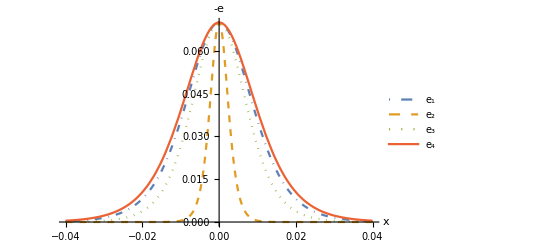

```mathematica
Amp=-0.07;
fig=Plot[{-u1[Amp], -u12[Amp],-u2[Amp], -u3[Amp]}, {x, -0.04, 0.04}, 
PlotLegends->LineLegend[{Subscript[e, 1],Subscript[e, 2],Subscript[e, 3],Subscript[e, 4]},LabelStyle->Directive[Black,16]],
PlotStyle->{{DotDashed(*, Purple*)},{Dashed(*, Red*)},{Dotted(*, Black*)}, Solid},
AxesLabel->{x,-e},
BaseStyle->{FontSize->14}
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Fig3a.pdf",fig]
```

Fig3a.pdf

```mathematica
sbst1={a->(1+nu)/4,b->-(1+nu+nu^2)/2,d->(1+nu)/4};
sbst2={a-> (5-5nu-6 nu^2+4 nu^3)/(8(1-nu)),b->(-7+7nu+2 nu^2)/(8(1-nu)),d->1/4};
length[A_]=a (A β+3 c^2 ρ)^2+3 c^2 ρ (A b β+3 c^2 (b+d) ρ);
Plot[{length[A]/.sbst1,length[A]/.sbst2},{A,-0.2,0},PlotLegends->{"Our","Bostrom's"}]
```

-Graphics-

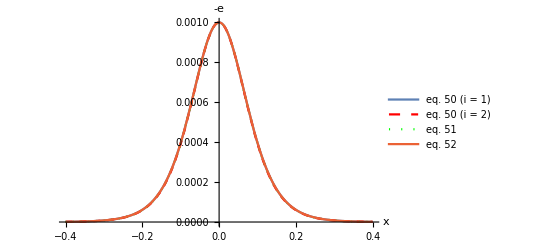

```mathematica
Amp=-0.001;
Plot[{-u1[Amp], -u12[Amp],-u2[Amp], -u3[Amp]}, {x, -0.4, 0.4}, 
AxesLabel->{x, -e},
PlotStyle->{Solid,{Dashed, Red},{Dotted, Green}}, PlotLegends->{"eq. 50 (i = 1)", "eq. 50 (i = 2)", "eq. 51", "eq. 52"}]
```

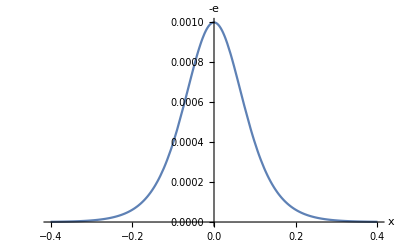

```mathematica
Amp=-0.001;
fig2=Plot[{-u1[Amp]}, {x, -0.4, 0.4}, 
AxesLabel->{x, -e},BaseStyle->{FontSize->14}
]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Fig3b.pdf",fig2]
```

Fig3b.pdf

### Dispersive curves

```mathematica
(* Our equation *)

DD1 =( 4/(nu+1) +  (2 (nu^2 + nu + 1))/(nu+1) k^2)^2 - 4 (4/(nu+1) + k^2) k^2;
Omega3a[k_] = Sqrt[2/(nu+1) + (nu^2 + nu + 1)/(nu+1) k^2 - Sqrt[DD1/4]];
Omega3b[k_]= Sqrt[2/(nu+1) + (nu^2 + nu + 1)/(nu+1) k^2 + Sqrt[DD1/4]];

(* Boestrom *)
rho=ρ;
lambda = E0 nu/ ((1+nu) (1 - 2 nu));
mu = E0/(2 (1+nu));
α1 = ((lambda^2 + 5 lambda mu + 5 mu^2) (3 lambda + 2 mu))/(2 (lambda+mu)^2 (lambda + 2 mu));
α2 = (6 lambda^2 + 21 lambda mu + 14 mu^2)/(2 (lambda+mu) (lambda + 2 mu));
DD2= (4  + α2 k^2)^2 - 4 α1 (4 + k^2) k^2;
Omega4a[k_] = Sqrt[(4 + α2 k^2 - Sqrt[DD2])/(2α1)];
Omega4b[k_] = Sqrt[(4 + α2 k^2 + Sqrt[DD2])/(2α1)];
```

```mathematica
(* DDE *)
Omega2[k_] = Sqrt[((1-(nu/2)  k^2) k^2)/(1 + (nu-1)(nu/2) k^2)];
(* Ostrovsky-Sutin *)
Omega1[k_] =Sqrt[k^2/(1 + (nu^2/2) k^2)];
```

```mathematica
kR=k R;
```

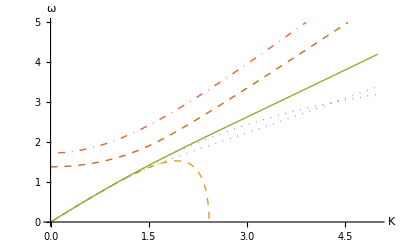

```mathematica
Plot[{Omega1[k],Omega2[k], Omega3a[k], Omega3b[k], 
Omega4a[k], Omega4b[k]}, {k, 0, 5}, AxesLabel->{K, ω},
PlotStyle->{{Dotted, Thick(*, Black*)},
{Dashed, Thick(*, Red*)},
{Solid, Thick(*, Blue*)},
{DotDashed, Thick(*, Purple*)}},
PlotRange->{0,5}]
```

```mathematica
(* Pochhammer - Chree, from Boestrom, scaled omega-> omega R/ c and k-> k/R *)
pk[ω_,k_] = ω Sqrt[rho/mu];
kp =  c ω /R  Sqrt[rho/(lambda + 2 mu)]

qs = Sqrt[ks^2 - k^2/ R^2]

qp = Sqrt[kp^2 - k^2 / R^2]
```

163.707 ω

80.6038 ω

√(-10000 k^2+26800. ω^2)

√(-10000 k^2+6496.97 ω^2)

```mathematica
Disp = ((ks^2 - 2 kp^2) BesselJ[0, qp R] + 2 qp^2  (D[BesselJ[1, x], x]/. x-> qp R)) (ks^2 - 2 k^2/ R^2) BesselJ[1, qs R] + 4 k^2/ R^2 qp qs BesselJ[1, qp R]  (D[BesselJ[1, x], x]/. x-> qs R)
```

(-20000 k^2+26800. ω^2) BesselJ[1,1/100 √(-10000 k^2+26800. ω^2)] (13806.1 ω^2 BesselJ[0,1/100 √(-10000 k^2+6496.97 ω^2)]+(-10000 k^2+6496.97 ω^2) (BesselJ[0,1/100 √(-10000 k^2+6496.97 ω^2)]-BesselJ[2,1/100 √(-10000 k^2+6496.97 ω^2)]))+20000 k^2 √(-10000 k^2+6496.97 ω^2) √(-10000 k^2+26800. ω^2) BesselJ[1,1/100 √(-10000 k^2+6496.97 ω^2)] (BesselJ[0,1/100 √(-10000 k^2+26800. ω^2)]-BesselJ[2,1/100 √(-10000 k^2+26800. ω^2)])

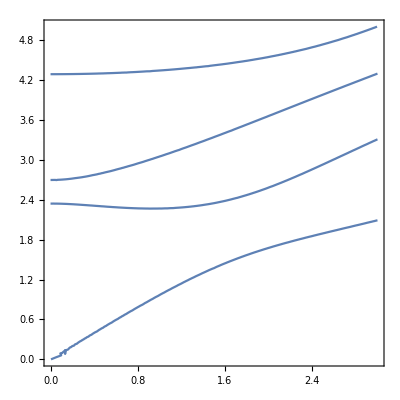

```mathematica
ContourPlot[{Disp==0, Dispexact==0}, {k, 0, 3}, {ω, 0, 5}]
```

```mathematica
(* As contour plots *)
G1 = ω^2 - k^2/(1 + (nu^2/2) k^2)

G2 =ω^2  - ((1-nu/2 k^2) k^2)/(1 + (nu (nu-1))/2 k^2)

G3 = ω^4 - ( 4/(nu+1) +  (2 (nu^2 + nu + 1))/(nu+1) k^2) ω^2  + (4/(nu+1) + k^2) k^2

G4 = α1 ω^4  - (4 + α2 k^2) ω^2 + (4 + k^2) k^2
```

-k^2/(1+0.0578 k^2)+ω^2

-(k^2 (1-0.17 k^2))/(1-0.1122 k^2)+ω^2

k^2 (2.98507+k^2)-(2.98507+2.17254 k^2) ω^2+ω^4

k^2 (4+k^2)-(4+3.32485 k^2) ω^2+2.09365 ω^4

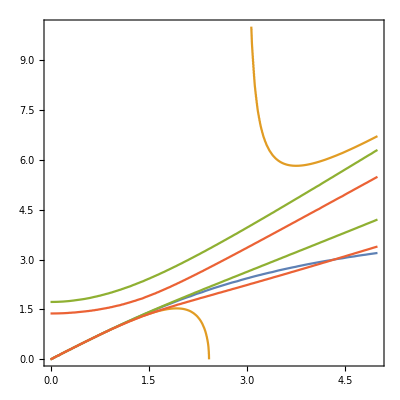

```mathematica
ContourPlot[{G1==0,G2 == 0, G3==0, G4==0}, {k, 0, 5}, {ω, 0, 10}]
```

```mathematica
(* Pochhammer - Chree, from Dai and Fan, scaled omega-> omega R/ C and k-> k/R *)
p = First[Sqrt[(rho c^2 ω^2)/((lambda + 2 mu) R^2) - k^2/R^2]]

q = First[Sqrt[(rho c^2 ω^2)/(mu R^2) - k^2/R^2]]
```

-10000 k^2+6496.97 ω^2

-10000 k^2+26800. ω^2

```mathematica
Dispexact=First[2 p / R (q^2 + k^2/ R^2 ) BesselJ[1, p R] BesselJ[1, q R] - (q^2 - k^2/ R^2 )^2 BesselJ[0, p R] BesselJ[1, q R] - 4 k^2/R^2 p q BesselJ[1,p R] BesselJ[0, q R]]
```

-40000 k^2 (-10000 k^2+6496.97 ω^2) (-10000 k^2+26800. ω^2) BesselJ[0,1/100 (-10000 k^2+26800. ω^2)] BesselJ[1,1/100 (-10000 k^2+6496.97 ω^2)]

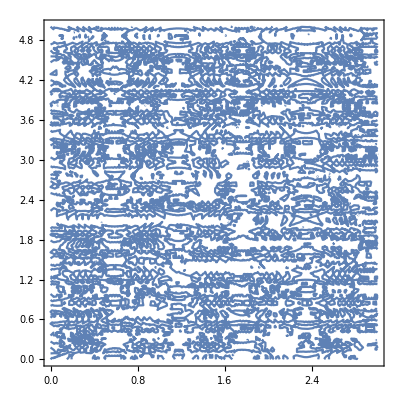

```mathematica
ContourPlot[Dispexact== 0, {k, 0, 3}, {ω,0, 5}]
```

```mathematica
Needs["PacletManager`"]
PacletInstall["~/Documents/MaTeX-1.7.5.paclet"]
```

Paclet[MaTeX,1.7.5,<>]

```mathematica
<<MaTeX`
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

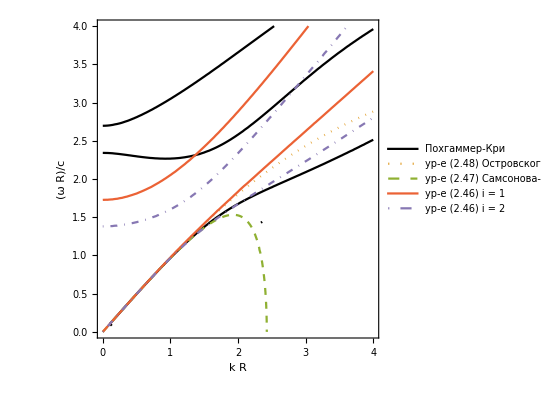

```mathematica
cp=ContourPlot[{Disp==0, G1==0,G2 == 0, G3==0, G4==0}, {k, 0, 4}, {ω, 0, 4}, 
ContourStyle->{{Solid, Thin, Black}, 
{Dotted, Thick(*, Black*)},{Dashed, Thick(*, Red*)},
{Solid, Thick(*, Blue*)},{DotDashed, Thick(*, Purple*)}},
PlotLegends->LineLegend[{"Похгаммер-Кри",
"ур-е (2.48) Островского-Сутина",
"ур-е (2.47) Самсонова-Порубова","ур-е (2.46) i = 1","ур-е (2.46) i = 2"},LabelStyle->Directive[Black,15]]];
figDisp=Show[cp,Axes->True,Frame->True,
FrameLabel->{"k R", Style["(ω R)/c",ScriptLevel->0]},
RotateLabel->False,
BaseStyle->{FontSize->14}]
```

```mathematica
(* Legend: Disp - Pochhamme-Chree, G1 - Ostrovsky-Sutin (Love), G2 - DDE (Bishop...), G3 - our equation, G4 - Bostroem *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["Fig2.pdf",figDisp]
```

Fig2.pdf

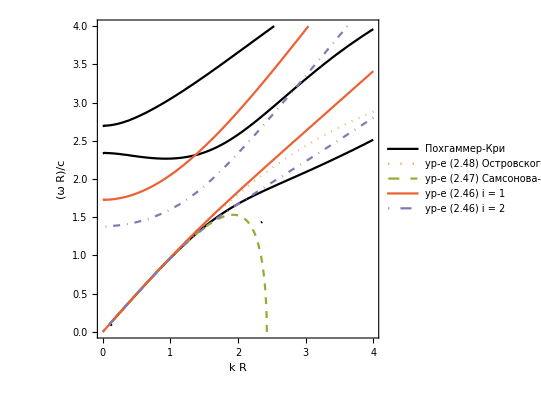

```mathematica
cp=ContourPlot[{Disp/k==0, G1/k==0,G2/k == 0, G3/k==0, G4/k==0}, {k, 0, 4}, {ω, 0, 4}, 
ContourStyle->{{Solid, Thin, Black}, 
{Dotted, Thick(*, Black*)},{Dashed, Thick(*, Red*)},
{Solid, Thick(*, Blue*)},{DotDashed, Thick(*, Purple*)}},
PlotLegends->LineLegend[{"Похгаммер-Кри",
"ур-е (2.48) Островского-Сутина",
"ур-е (2.47) Самсонова-Порубова","ур-е (2.46) i = 1","ур-е (2.46) i = 2"},LabelStyle->Directive[Black,15]]];
figDisp2=Show[cp,Axes->True,Frame->True,
FrameLabel->{"k R", Style["(ω R)/c",ScriptLevel->0]},
RotateLabel->False,
BaseStyle->{FontSize->14}]
```

```mathematica
(* Phase vesocities *)
V1 = v^2 k - k/(1 + (nu^2/2) k^2);
V2 =v^2k  - ((1-nu/2 k^2) k)/(1 + (nu (nu-1))/2 k^2);
V3 = v^4k^3 - ( 4/(nu+1) +  (2 (nu^2 + nu + 1))/(nu+1) k^2) v^2k  + (4/(nu+1) + k^2) k;

V4 = α1 v^4 k^3  - (4 + α2 k^2) v^2 k + (4 + k^2) k;
```

```mathematica
(* Pochhammer - Chree, from Boestrom, scaled omega-> omega R/ c and k-> k/R *)
k2s = c v/ R  Sqrt[rho/mu]k;

k2p =  c v /R  Sqrt[rho/(lambda + 2 mu)]k;

q2s = Sqrt[k2s^2 - k^2/ R^2];

q2p = Sqrt[k2p^2 - k^2 / R^2];
```

```mathematica
DispV = ((k2s^2 - 2 k2p^2) BesselJ[0, q2p R] + 2 q2p^2  (D[BesselJ[1, x], x]/. x-> q2p R))(k2s^2 - 2 k^2/ R^2) BesselJ[1, q2s R]+ 4 k^2/ R^2 q2p q2s BesselJ[1, q2p R]  (D[BesselJ[1, x], x]/. x-> q2s R)//Simplify;
```

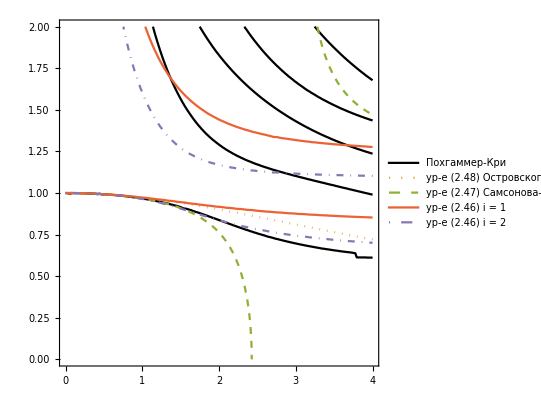

```mathematica
cp=ContourPlot[{DispV==0, V1==0,V2== 0, V3==0, V4==0}, {k, 0, 4}, {v, 0, 2}, 
ContourStyle->{{Solid, Thin, Black}, 
{Dotted, Thick(*, Black*)},{Dashed, Thick(*, Red*)},
{Solid, Thick(*, Blue*)},{DotDashed, Thick(*, Purple*)}},
PlotLegends->LineLegend[{"Похгаммер-Кри",
"ур-е (2.48) Островского-Сутина",
"ур-е (2.47) Самсонова-Порубова","ур-е (2.46) i = 1","ур-е (2.46) i = 2"},LabelStyle->Directive[Black,15]]]
```

```mathematica
Solve[Disp==0,{ω,k}]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[(-20000 k^2+26800. ω^2) BesselJ[1,1/100 √(-10000 k^2+26800. ω^2)] (13806.1 ω^2 BesselJ[0,1/100 √(-10000 k^2+6496.97 ω^2)]+(-10000 k^2+6496.97 ω^2) (BesselJ[0,1/100 √(-10000 k^2+6496.97 ω^2)]-BesselJ[2,1/100 √(-10000 k^2+6496.97 ω^2)]))+20000 k^2 √(-10000 k^2+6496.97 ω^2) √(-10000 k^2+26800. ω^2) BesselJ[1,1/100 √(-10000 k^2+6496.97 ω^2)] (BesselJ[0,1/100 √(-10000 k^2+26800. ω^2)]-BesselJ[2,1/100 √(-10000 k^2+26800. ω^2)])==0,{ω,k}]